This file produces the equations_of_state functions.

#### Utils

```mathematica
numrepl = {Δ[r]-> delta, Δ'[r]-> deltap, Δ''[r]-> deltapp, ω->omega,ϵ->epsilon, t2[r]->t2, t2'[r]->t2p, t2''[r]->t2pp,S[r,ms]->S[ms],Derivative[1,0][S][r,ms]->Sp[ms],Derivative[2,0][S][r,ms]->Spp[ms],B[r,mb]->Bs[mb],Derivative[1,0][B][r,mb]->Bsp[mb],Derivative[2,0][B][r,mb]->Bspp[mb],P[r]->P,P'[r]->Pp,P''[r]->Ppp,q[r]->q, q'[r]->qp, 
(* kinetic profiles *)
β[r]->beta,β'[r]->betap,Ah[r]->Ah,Ah'[r]->Ahp,Μ2[r]-> mach2, Μ2'[r]->mach2p,Bc[r]->Bc,Bc'[r]->Bcp};
ToMatlab[expr_,indexed_:False]:=Module[{str,processed},(*First extract expression if it's a Piecewise or List*)processed=expr;
If[Head[processed]===Piecewise,processed=processed[[1,1,1]]; (*Take the first branch expression*)];
If[Head[processed]===List,processed=First[processed]; (*Take first element if it's a list*)];
str=ToString[processed/. numrepl,FortranForm];
str=StringReplace[str,{"\n"->" ","\r"->" ","\t"->" "}];
str=StringTrim[StringReplace[str,RegularExpression["\\s+"]->" "]];
(*trigonometric functions and vectorized operations*)str=StringReplace[str,{"Cos"->"cos","Sin"->"sin","Csc"->"csc","**"->".^","*"->".*","/"->"./","Sqrt"->"sqrt"}];
(*exponentials*)str=StringReplace[str,{RegularExpression["\\bE\\.\\^\\("]->"exp(",RegularExpression["\\bE\\^\\("]->"exp("}];
(*Conditionals*)str=StringReplace[str,{RegularExpression["\\b.ge.\\b"]->" >= ",RegularExpression["\\b.lt.\\b"]->" < "}];
(*Apply indexing if requested*)If[indexed,str=StringReplace[str,{"BB"->"BB(idx)","RR"->"RR(idx)", "betap"->"betap(idx)","beta"->"beta(idx)", "Bcp"->"Bcp(idx)","Bc"->"Bc(idx)", "Ahp"->"Ahp(idx)","Ah"->"Ah(idx)"}];];
StringTrim[str]]
```

## Equations of state

```mathematica
(* Fully parallel, rotating *)
betapar[r_,B_,R_]= β[r]B Exp[(R^2-1)Μ2[r]];
```

```mathematica
(* Isotropic Rotating*)
betapar[r_,B_,R_]= β[r] Exp[(R^2-1)Μ2[r]];
```

```mathematica
(* Isotropic *)
betapar[r_,B_,R_]= β[r];
```

```mathematica
(* modified bi-Maxwellian *)
betapar[r_,B_,R_] = Piecewise[{{β[r] B/(Ah[r]B-((Ah[r]-1)Bc[r])),B>=Bc[r]}, {β[r](2 (Ah[r](1-B/Bc[r]))^(1/2)/Bc[r]+(Ah[r]B - (1+Ah[r]-2(Ah[r](1-B/Bc[r]))^(1/2))Bc[r])/(Ah[r]^2(B-Bc[r])^2-Bc[r]^2)),B<Bc[r]}}];
```

```mathematica
betapar[r_,B_,R_] = Piecewise[{{β[r] (B/Bc[r])/(1-Ah[r](1-B/Bc[r])),B>=Bc[r]}, {β[r](B/Bc[r](1+Ah[r](1-B/Bc[r])-2(Ah[r](1-B/Bc[r]))^(5/2))/(1-Ah[r]^2(1-B/Bc[r])^2)),B<Bc[r]}}];
```

```mathematica
Limit[β[r](B/Bc[r](1+Ah[r](1-B/Bc[r])-2(Ah[r](1-B/Bc[r]))^(5/2))/((1-Ah[r](1-B/Bc[r]))(1+Ah[r](1-B/Bc[r])))),Bc[r]->B]
Limit[β[r] (B/Bc[r])/(1-Ah[r](1-B/Bc[r])),Bc[r]->B]
```

β[r]

β[r]

```mathematica
Limit[betapar[r,B,R],Ah[r]->0]
Limit[betapar[r,B,R]-B Derivative[0,1,0][betapar][r,B,R],Ah[r]->0]
Limit[betapar[r,B,R],Ah[r]->∞]
Limit[betapar[r,B,R]-B Derivative[0,1,0][betapar][r,B,R],Ah[r]->∞]
```

(B β[r])/Bc[r]

0

Piecewise[{{B DirectedInfinity[(1/Sign[Bc[r]])^(3/2)] β[r], B<Bc[r]}, {0, True}}]

Piecewise[{{(B^2 DirectedInfinity[√(1/Sign[Bc[r]])] β[r])/Bc[r], B<Bc[r]}, {0, True}}]

```mathematica
Derivative[0,1,0][betapar][r,B,R]// Simplify
```

Piecewise[{{-((-1+Ah[r]) Bc[r] β[r])/(Ah[r] (B-Bc[r])+Bc[r])^2, Bc[r]≤B}, {1/(Bc[r] (-Ah[r]^2 (B-Bc[r])^2+Bc[r]^2)^2)(Ah[r]^4 √(Ah[r] (1-B/Bc[r])) (3 B-2 Bc[r]) (B-Bc[r])^3-Ah[r]^3 (B-Bc[r])^2 Bc[r]^2+Bc[r]^4+Ah[r] Bc[r]^3 (-2 B+Bc[r])-Ah[r]^2 (B-Bc[r]) Bc[r]^2 (B (-1+7 √(Ah[r] (1-B/Bc[r])))+(-1-2 √(Ah[r] (1-B/Bc[r]))) Bc[r])) β[r], Bc[r]>B}, {0, True}}]

```mathematica
betapar[0,B,0]-B Derivative[0,1,0][betapar][0,B,0] /. {B-> B B0,Bc[0]-> Bc[0] B0}// Simplify
betapar[0,B,0]-B Derivative[0,1,0][betapar][0,B,0]// Simplify
```

Piecewise[{{(B^2 Ah[0] β[0])/(B Ah[0]+Bc[0]-Ah[0] Bc[0])^2, B B0≥B0 Bc[0]}, {-(B^2 (B^3 Ah[0]^4 √(Ah[0] (1-B/Bc[0]))-B^2 Ah[0]^3 (1+3 Ah[0] √(Ah[0]-(B Ah[0])/Bc[0])) Bc[0]+B Ah[0]^2 (2+2 Ah[0]-5 √(Ah[0]-(B Ah[0])/Bc[0])+3 Ah[0]^2 √(Ah[0]-(B Ah[0])/Bc[0])) Bc[0]^2-Ah[0] (1+Ah[0]^2+Ah[0] (2-5 √(Ah[0]-(B Ah[0])/Bc[0]))+Ah[0]^3 √(Ah[0]-(B Ah[0])/Bc[0])) Bc[0]^3) β[0])/(Bc[0] (B^2 Ah[0]^2-2 B Ah[0]^2 Bc[0]+(-1+Ah[0]^2) Bc[0]^2)^2), B B0<B0 Bc[0]}, {0, True}}]

Piecewise[{{(B^2 Ah[0] β[0])/(B Ah[0]+Bc[0]-Ah[0] Bc[0])^2, B≥Bc[0]}, {-(B^2 (B^3 Ah[0]^4 √(Ah[0] (1-B/Bc[0]))-B^2 Ah[0]^3 (1+3 Ah[0] √(Ah[0]-(B Ah[0])/Bc[0])) Bc[0]+B Ah[0]^2 (2+2 Ah[0]-5 √(Ah[0]-(B Ah[0])/Bc[0])+3 Ah[0]^2 √(Ah[0]-(B Ah[0])/Bc[0])) Bc[0]^2-Ah[0] (1+Ah[0]^2+Ah[0] (2-5 √(Ah[0]-(B Ah[0])/Bc[0]))+Ah[0]^3 √(Ah[0]-(B Ah[0])/Bc[0])) Bc[0]^3) β[0])/(Bc[0] (B^2 Ah[0]^2-2 B Ah[0]^2 Bc[0]+(-1+Ah[0]^2) Bc[0]^2)^2), B<Bc[0]}, {0, True}}]

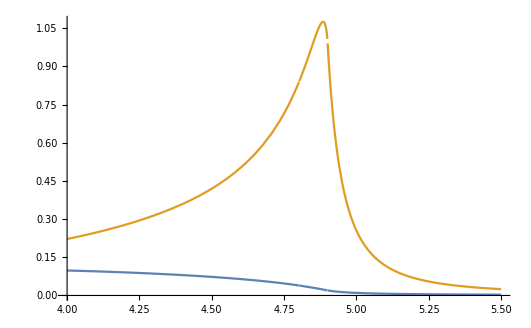

```mathematica
Plot[Evaluate[{betapar[0,B,0],betapar[0,B,0]-B Derivative[0,1,0][betapar][0,B,0]}/Ah[0] /. {Bc[0]->4.9, Ah[0]->50,β[0]->1}], {B,4,5.5}, PlotRange->Full]
```

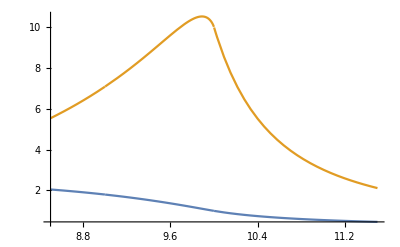

```mathematica
Plot[Evaluate[{betapar[0,B,0],betapar[0,B,0]-B Derivative[0,1,0][betapar][0,B,0]} /. {Bc[0]->10, Ah[0]->10,β[0]->1}], {B,8.5,11.5}, PlotRange->Full]
```

## Write to Matlab

```mathematica
kinprofiles = {"beta", "Ah", "mach2","Bc"};
presentProfiles = Select[kinprofiles, StringContainsQ[ToMatlab[betapar[r,BB,RR]],#]&];
```

```mathematica
WriteMatlab[fileName_String,funcName_String]:=Module[{stream,outList,first7,derivSpecs,bp,isPW,bp1,bp2,condStr,results,assocDef,assocAlt,headerLine,i,d,s1,s2,name,maxLen,parts,current,chars},outList={"dbetapardB0","dbetapardr","dbetapardB","dbetapardR","d2betapardB2","d2betapardrdB","d2betapardRdB","d2betapardrdR","d2betapardR2","d3betapardrdB2","d3betapardB3","d3betapardBdR2","d3betapardB2dR","d3betapardrdRdB","betapar","betaperp"};
first7=outList[[1;;7]];
derivSpecs={{{1,0,0},"dbetapardr"},{{0,1,0},"dbetapardB"},{{0,0,1},"dbetapardR"},{{0,2,0},"d2betapardB2"},{{1,1,0},"d2betapardrdB"},{{0,1,1},"d2betapardRdB"},{{1,0,1},"d2betapardrdR"},{{0,0,2},"d2betapardR2"},{{1,2,0},"d3betapardrdB2"},{{0,3,0},"d3betapardB3"},{{0,1,2},"d3betapardBdR2"},{{0,2,1},"d3betapardB2dR"},{{1,1,1},"d3betapardrdRdB"}};
(*Extract base function and handle Piecewise*)bp=betapar[r,BB,RR];
isPW=Head[bp]===Piecewise;
If[isPW,bp1=bp[[1,1,1]];(*First branch expression*)bp2=bp[[1,2,1]];(*Second branch expression*)condStr=ToMatlab[bp[[1,2,2]]];  (*Condition*),bp1=bp;
bp2=.;
condStr=.;];
(*Pre-simplify once*)bp1=Simplify[bp1];
If[isPW,bp2=Simplify[bp2]];
results=Table[Module[{a=derivSpecs[[i,1,1]],b=derivSpecs[[i,1,2]],c=derivSpecs[[i,1,3]],nm=derivSpecs[[i,2]],d,d1,d2},If[isPW,(*For Piecewise:compute derivatives for both branches*)d1=Quiet[Check[Derivative[a,b,c][betapar][r,BB,RR]/. betapar[r,BB,RR]->bp1,0]];
d2=Quiet[Check[Derivative[a,b,c][betapar][r,BB,RR]/. betapar[r,BB,RR]->bp2,0]];
s1=ToMatlab[Simplify[d1]];
s2=ToMatlab[Simplify[d2],True]; (*Use indexing for second branch*),(*For non-Piecewise:standard computation*)d=Quiet[Check[Derivative[a,b,c][betapar][r,BB,RR],0]];
s1=ToMatlab[Simplify[d]];
s2="";];
s1=If[StringTrim[s1]===""||StringTrim[s1]==="0","zeros(size(RR))",s1];
s2=If[StringTrim[s2]===""||StringTrim[s2]==="0","zeros(size(RR))",s2];
{nm,s1,s2}],{i,Length[derivSpecs]}];
assocDef=AssociationThread[results[[All,1]]->results[[All,2]]];
assocAlt=AssociationThread[results[[All,1]]->results[[All,3]]];
stream=OpenWrite[fileName];
maxLen=80;
line="function [";
chars=StringLength[line];
parts={};
current={};
Scan[(AppendTo[current,#];
chars+=StringLength[#]+If[current==={},0,2];
If[chars>maxLen,AppendTo[parts,StringRiffle[Most[current],", "]<>", ...\n    "<>Last[current]];
current={};
chars=4+StringLength[#];])&,outList];
If[current=!={},AppendTo[parts,StringRiffle[current,", "]]];
headerLine="function ["<>StringRiffle[parts,", "]<>"] = "<>funcName<>"(kinetic_profiles,r,RR,BB)\n";
WriteString[stream,headerLine];
(*Write kinetic profiles*)
If[Length[presentProfiles]>0,If[isPW,Do[WriteString[stream,"    "<>presentProfiles[[i]]<>" = kinetic_profiles."<>presentProfiles[[i]]<>"(r) * ones(1,size(RR,2));\n"];
WriteString[stream,"    "<>presentProfiles[[i]]<>"p = kinetic_profiles."<>presentProfiles[[i]]<>"p(r) * ones(1,size(RR,2));\n"];,{i,1,Length[presentProfiles]}];,Do[WriteString[stream,"    "<>presentProfiles[[i]]<>" = kinetic_profiles."<>presentProfiles[[i]]<>"(r);\n"];
WriteString[stream,"    "<>presentProfiles[[i]]<>"p = kinetic_profiles."<>presentProfiles[[i]]<>"p(r);\n"];,{i,1,Length[presentProfiles]}];];];
(*Write condition for Piecewise case*)
If[isPW,WriteString[stream,"    idx = "<>condStr<>";\n"];];
(*Write first 7 derivatives*)
Do[name=first7[[i]];
If[name=!="dbetapardB0",WriteString[stream,"    "<>name<>" = "<>assocDef[name]<>";\n"];
If[isPW&&StringTrim[assocAlt[name]]=!=""&&StringTrim[assocAlt[name]]=!=assocDef[name],WriteString[stream,"    "<>name<>"(idx) = "<>assocAlt[name]<>";\n"];]],{i,Length[first7]}];
WriteString[stream,"    dbetapardB0 = dbetapardB(1,1);\n"];
WriteString[stream,"    if nargout > 7 % Jacobian computation\n"];
(*Write remaining derivatives*)Do[name=outList[[i]];
If[name=!="dbetapardB0"&&!MemberQ[first7,name],WriteString[stream,"        "<>name<>" = "<>assocDef[name]<>";\n"];
If[isPW&&StringTrim[assocAlt[name]]=!=""&&StringTrim[assocAlt[name]]=!=assocDef[name],WriteString[stream,"        "<>name<>"(idx) = "<>assocAlt[name]<>";\n"];]],{i,8,Length[outList]-2}];
WriteString[stream,"        if nargout > 13 % postprocessing\n"];
(*Write betapar and betaperp*)If[isPW,WriteString[stream,"            betapar = "<>ToMatlab[bp1]<>";\n"];
WriteString[stream,"            betapar(idx) = "<>ToMatlab[bp2,True]<>";\n"];
(*Compute derivative for betaperp*)d1=Simplify[Derivative[0,1,0][betapar][r,BB,RR]/. betapar[r,BB,RR]->bp1];
d2=Simplify[Derivative[0,1,0][betapar][r,BB,RR]/. betapar[r,BB,RR]->bp2];
WriteString[stream,"            betaperp = betapar - BB.*("<>ToMatlab[d1]<>");\n"];
WriteString[stream,"            betaperp(idx) = betapar(idx) - BB(idx).*("<>ToMatlab[d2,True]<>");\n"];,WriteString[stream,"            betapar   = "<>ToMatlab[Simplify[betapar[r,BB,RR]]]<>";\n"];
WriteString[stream,"            betaperp  = "<>ToMatlab[Simplify[betapar[r,BB,RR]-BB Derivative[0,1,0][betapar][r,BB,RR]]]<>";\n"];];
WriteString[stream,"        end\n    end\nend\n"];
Close[stream];
Print["Wrote MATLAB file \"",fileName,"\" with <",funcName,">."];]
```

```mathematica
WriteMatlab["/home/vanparys/Documents/PhD/Codes/EQUIL/src/equations_of_state/isotropic_rotating.m","isotropic_rotating"]
```

Wrote MATLAB file "/home/vanparys/Documents/PhD/Codes/EQUIL/src/equations_of_state/isotropic_rotating.m" with <isotropic_rotating>.

```mathematica
WriteMatlab["/home/vanparys/Documents/PhD/Codes/EQUIL/src/equations_of_state/parallel_rotating.m","parallel_rotating"]
```

Wrote MATLAB file "/home/vanparys/Documents/PhD/Codes/EQUIL/src/equations_of_state/parallel_rotating.m" with <parallel_rotating>.

```mathematica
WriteMatlab["/home/vanparys/Documents/PhD/Codes/EQUIL/src/equations_of_state/isotropic.m","isotropic"]
```

Wrote MATLAB file "/home/vanparys/Documents/PhD/Codes/EQUIL/src/equations_of_state/isotropic.m" with <isotropic>.

```mathematica
WriteMatlab["/home/vanparys/Documents/PhD/Codes/EQUIL/src/equations_of_state/biMaxwellian.m","biMaxwellian"]
```

Wrote MATLAB file "/home/vanparys/Documents/PhD/Codes/EQUIL/src/equations_of_state/biMaxwellian.m" with <biMaxwellian>.